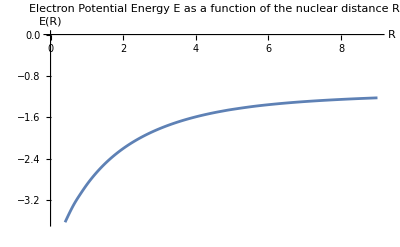

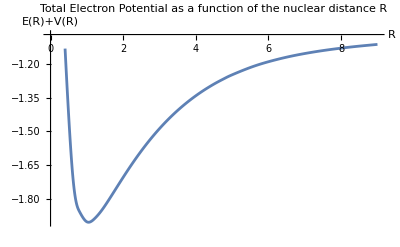

```mathematica
eee:= {{0.4,-3.63220035763749},{0.6000000000000001,-3.342967657169881},{0.8,-3.108958641062607},{1.,-2.903572071237722},{1.2,-2.724615379110777},{1.4000000000000001,-2.5685373136579623},{1.6,-2.4318739605980806},{1.8,-2.3116176070067165},{2.,-2.205268141074433},{2.2,-2.1107695087373237},{2.4000000000000004,-2.0264405155856062},{2.6000000000000005,-1.9508966052031411},{2.8000000000000003,-1.8829976855861281},{3.0000000000000004,-1.8217919230074089},{3.2,-1.7664850132944716},{3.4000000000000004,-1.7164029887912562},{3.6000000000000005,-1.6709739195407665},{3.8000000000000003,-1.6297050156560733},{4.,-1.5921695002140073},{4.2,-1.557994793837561},{4.4,-1.5268516153151768},{4.6000000000000005,-1.4984480258936026},{4.800000000000001,-1.472522800588277},{5.000000000000001,-1.4488405856146125},{5.5,-1.3980992756498476},{6.,-1.3572714059906277},{6.5,-1.324123072854079},{7.,-1.2969021523389976},{7.5,-1.2742525473704893},{8.,-1.2551405664179884},{8.5,-1.2387882439117885},{9.,-1.2246129328204522}};

v[r_]:=1/r;

totalE = Map[{#[[1]],v[#[[1]]]+#[[2]] }&,eee];

(*totalE*)

ListLinePlot[eee,AxesLabel->{"R","E(R)"},InterpolationOrder->3, PlotLabel->"Electron Potential Energy E as a function of the nuclear distance R"]

Print[""]

ListLinePlot[totalE,AxesLabel->{"R","E(R)+V(R)"},InterpolationOrder->3,PlotLabel->"Total Electron Potential as a function of the nuclear distance R"]
```